## Nonlinear observer for the van der Pol oscillator Problem 7.17

```mathematica
Clear["Global`*"];
```

Full nonlinear observer

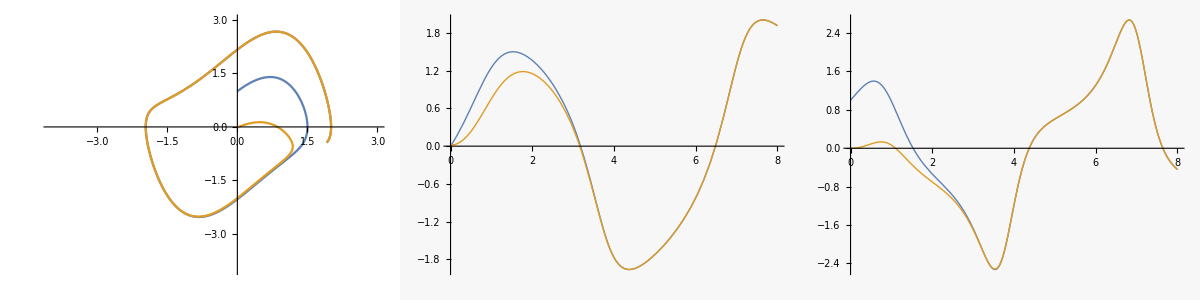

```mathematica
f[L1_,tend_,initval_]:=Module[{eq1,eq2,init1,init2,x1,x2,xh1,xh2,L2,t},
L2=1/4 (-3+2 L1+L1^2-2 xh1[t]^2-2 L1 xh1[t]^2+xh1[t]^4-8 xh1[t] xh2[t]);
eq1={x1'[t]==x2[t],x2'[t]==ϵ (1-x1[t]^2)x2[t]-x1[t]};
eq2={xh1'[t]==xh2[t]+ L1(x1[t]-xh1[t]),xh2'[t]==ϵ (1-xh1[t]^2)xh2[t]-xh1[t]+ L2(x1[t]-xh1[t])};
init1={x1[0]==0,x2[0]==initval};
init2={xh1[0]==0.02,xh2[0]==0};
NDSolveValue[{eq1,eq2,init1,init2},{x1,x2,xh1,xh2},{t,0,tend}]]

tend=8; ϵ=1; L1=2; initval=1;{x1sol,x2sol,xh1sol,xh2sol}=f[L1,tend,initval];
p1=ParametricPlot[{{x1sol[t],x2sol[t]},{xh1sol[t],xh2sol[t]}},{t,0,tend},PlotRange->{-4,3},ImageSize->200];
p2=Plot[{x1sol[t],xh1sol[t]},{t,0,tend},ImageSize->200];
p3=Plot[{x2sol[t],xh2sol[t]},{t,0,tend},PlotRange->All,ImageSize->200];
Grid[{{p1,p2,p3}},Spacings->2]
```

Export data

```mathematica
x1solt=Table[x1sol[t],{t,0,tend,0.01}];
x2solt=Table[x2sol[t],{t,0,tend,0.01}];
xh1solt=Table[xh1sol[t],{t,0,tend,0.01}];
xh2solt=Table[xh2sol[t],{t,0,tend,0.01}];
(* 
SetDirectory[NotebookDirectory[]];
Export["vdPobserver.dat",Flatten/@Transpose[{x1solt,x2solt,xh1solt,xh2solt}],"Table"];
*)
```

Nonlinear observer calculations

```mathematica
Clear[L1];a=({{-L1, 1}, {-1-L2-2ϵ x1 x2, ϵ(1-x1^2)}});Eigenvalues[a]//Simplify
```

{1/2 (1-L1-x1^2-√(-3+2 L1+L1^2-4 L2-2 x1^2-2 L1 x1^2+x1^4-8 x1 x2)),1/2 (1-L1-x1^2+√(-3+2 L1+L1^2-4 L2-2 x1^2-2 L1 x1^2+x1^4-8 x1 x2))}

```mathematica
L2s=Solve[-3+2 L1+L1^2-4 L2-2 x1^2-2 L1 x1^2+x1^4-8 x1 x2==0,{L1,L2}][[1,1]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

L2→1/4 (-3+2 L1+L1^2-2 x1^2-2 L1 x1^2+x1^4-8 x1 x2)

```mathematica
a1=a/.L2s//Simplify; MatrixForm[a1]
```

(-L1 | 1
-1/4 (1+L1-x1^2)^2 | 1-x1^2)

```mathematica
Eigenvalues[a1]
```

{1/2 (1-L1-x1^2),1/2 (1-L1-x1^2)}

```mathematica
L2func[L1_]:=1/4 (-3+2 L1+L1^2-2 x1^2-2 L1 x1^2+x1^4-8 x1 x2)
L2func[2]
```

1/4 (5-6 x1^2+x1^4-8 x1 x2)